```mathematica
Quit[];
```

```mathematica
Needs["QuantumManyBody`"]
```

```mathematica
latticeSize = 10;
length = 2^latticeSize;
```

### The Heisenberg model

```mathematica
listCouplings = Partition[Range @ latticeSize , 2 , 1 , 1];
```

```mathematica
listGraphCoefficients = {listCouplings , ({1 , 1 , 1} &) /@ Range @ Length @ listCouplings}
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
{hamiltonianDecomposed , hamiltonian} = SpinChainHamiltonian @@ listGraphCoefficients;
```

```mathematica
groundStateHeisenberg = Chop[FindGroundState @ hamiltonian, 10^-8];
groundEnergyHeisenberg = EnergyStored[groundStateHeisenberg , hamiltonian]
```

-18.0618

```mathematica
β = 3.;
Δt = 0.1;
```

```mathematica
initialState = SparseArray[((Position[#,Min[#]]&) @ Normal @ Diagonal @ hamiltonian)[[1 ]] -> 1. , {2^latticeSize} , 0];
```

```mathematica
dD = 1;
```

```mathematica
evolvedKetHeisenberg = QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , dD];
```

```mathematica
energyHeisenberg = ({#1 ,1/groundEnergyHeisenberg * Conjugate @ #2 . hamiltonian . #2} &)@@@ evolvedKetHeisenberg ;
```

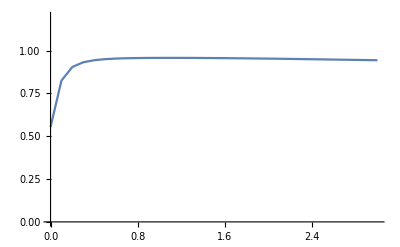

```mathematica
ListPlot[energyHeisenberg , Joined->True , PlotRange->{All , {0. , 1.2}}]
```

### The Heisenberg random model

```mathematica
listCouplings = Partition[Range @ latticeSize , 2 , 1 , 1];
```

```mathematica
listGraphCoefficients = {listCouplings , ({RandomReal[] , RandomReal[] , RandomReal[]} &) /@ Range @ Length @ listCouplings}
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}},{{0.198264,0.768072,0.146782},{0.814222,0.368924,0.836927},{0.0303474,0.0915315,0.65112},{0.316264,0.0110149,0.881819},{0.306733,0.486832,0.730299},{0.788704,0.467283,0.185244},{0.715869,0.934351,0.194832},{0.594017,0.83182,0.367776},{0.267322,0.7795,0.859934},{0.667586,0.44663,0.623894}}}

```mathematica
{hamiltonianDecomposed , hamiltonian} = SpinChainHamiltonian @@ listGraphCoefficients;
```

```mathematica
groundStateRandom = Chop[FindGroundState @ hamiltonian, 10^-8];
groundEnergyRandom = EnergyStored[groundStateHeisenberg , hamiltonian]
```

-9.24999

```mathematica
β = 3.;
Δt = 0.1;
```

```mathematica
initialState = SparseArray[((Position[#,Min[#]]&) @ Normal @ Diagonal @ hamiltonian)[[1 ]] -> 1. , {2^latticeSize} , 0];
```

```mathematica
dD = 1;
```

```mathematica
evolvedKetRandom = QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , dD];
```

General::munfl: 8.00465×10^-159 2.47555×10^-164 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
energyRandom = ({#1 ,1/groundEnergyRandom * Conjugate @ #2 . hamiltonian . #2} &)@@@ evolvedKetRandom ;
```

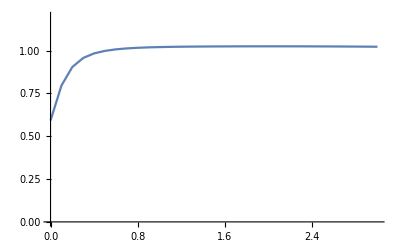

```mathematica
ListPlot[energyRandom, Joined->True , PlotRange->{All , {0. , 1.2}}]
```

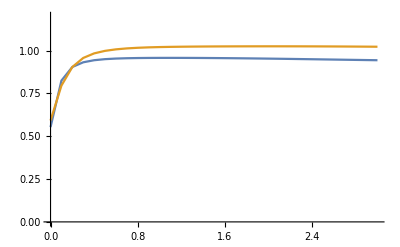

```mathematica
ListPlot[{energyHeisenberg , energyRandom}, Joined->True , PlotRange->{All , {0. , 1.2}}]
```